```mathematica
Remove[x]
n :=8
m:=1
a:=1/2
Subscript[E, 0]:=1/2
A:=(m/(2*π*a))^(n/2)
V[x_]:=x^2/2
Subscript[x, 0]:= 0
Subscript[x, n]:=Subscript[x, 0]
S[x_]:=∑_(j=0)^(n-1) (m/(2*a)(Subscript[x, j+1]-Subscript[x, j])^2+a*V[Subscript[x, j]])
YVals :=Table[Subscript[x, 0]:= 0.2*i; A*Integrate[E^(-S[x]),
{Subscript[x, 7], -∞, ∞}, {Subscript[x, 6], -∞, ∞},{Subscript[x, 5], -∞, ∞}, {Subscript[x, 4], -∞, ∞}, {Subscript[x, 3], -∞, ∞}, {Subscript[x, 2], -∞, ∞},{Subscript[x, 1], -∞, ∞}], 
												{i, 0, 10}]
Y[x_]:=ⅇ^(-a*n*Subscript[E, 0])/π^(1/2)ⅇ^(-x^2)
```

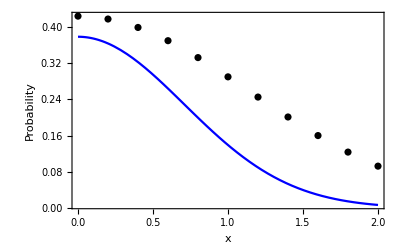
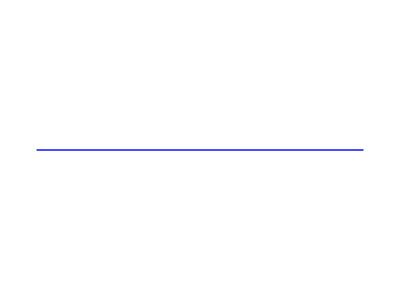
ShowLegend[-Graphics-,{{{  ●,Numerical},{-Graphics-,Analytical}},LegendPosition→{0.3,0.2},LegendSize→{0.65,0.25},LegendShadow→False}]

```mathematica
ShowLegend[Show[
{ListPlot[YVals,DataRange->{0,2}, PlotStyle -> {Black}], 
Plot[Y[x], {x, 0, 2}, PlotStyle ->{Blue}]},
Frame -> True,FrameLabel->{x, "Probability"}, PlotRange->All],
{{{Style["  ●",12,Black],"Numerical"},
{Graphics@{Thick, Blue,Line[{{1,0},{3,0}}]},"Analytical"}},
LegendPosition->{0.3,0.2}, LegendSize->{0.65,0.25}, LegendShadow ->False}]
```